ODVOD

Definicija:

```mathematica
Limit[(f(a+h)-f(a))/h,h->0];                         
Limit[(f(x)-f(a))/(x-a),x->a];
```

Primer izračuna odvoda po definiciji:

```mathematica
f[x_] := x^2
a = 3;
Limit[(f[x] - f[a])/(x-a),x->a]
```

6

Preverimo z odvodom:

```mathematica
D[f[x],x]/.x->a
```

6

Geometrijski pomen odvoda:
Odovod v točki predstavlja diferenčni koeficient, oziroma k ,tangente na graf funkcije (v tej točki).

```mathematica
ClearAll[f]
OdvodVTočki[f_,x0_,zac_,kon_]:=Module[{k0,enacba,rešitev,n0},
k0=D[f[x],x]/.x->x0;
enacba = f[x0]==k0 * x0+n;
rešitev = Solve[enacba,n];
n0=n/.rešitev //First;
Plot[{f[x],k0 *x+n0},{x,zac,kon}]]
```

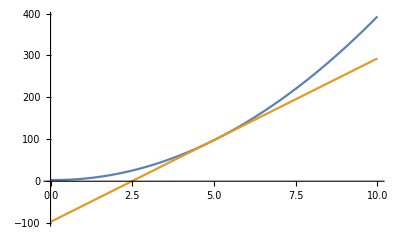

```mathematica
f [x_] := 4x^2 -x +3
OdvodVTočki[f,5,0,10]
```

```mathematica
ClearAll[a]
EnacbaTangente[f_]:=Module[{k,rešitev,g,n0,enacba},
k = D[f[x],x]/.x->a;
enacba = f[a] == k*a +n;
rešitev = Solve[enacba,n];
n0 = n/.rešitev //First;
k x + n0
]
```

```mathematica
GrafOdvoda[f_,zac_,kon_]:=Module[{},
enacba = EnacbaTangente[f];
g[x_,a_] =enacba;
Manipulate[Plot[{f[x],g[x,a]},{x,-5,5},PlotRange->{5,-5}],{a,zac,kon}]
]
```

```mathematica
f[x_]:=3x^3-4x^2 -2x+3
EnacbaTangente[f];
GrafOdvoda[f,-2,2]
```

Ekstremi:
Ekstreme lahko izračunamo z odvodom saj je k tangente na graf v ekstremu enak 0.

```mathematica
ekstremi[f_]:=Solve[D[f[x],x]==0,x]
```

```mathematica
f[x_] :=3x^3+ 2x^2 -19x + 12
```

```mathematica
GrafEkstremov[f_,zac_,kon_]:=Module[{ekst},
ekst = x/.ekstremi[f];
Plot[{f[x],f[ekst]},{x,zac,kon}]
]
```

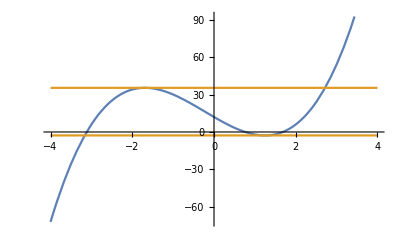

```mathematica
GrafEkstremov[f,-4,4]
```

Normale:
Normala na tangetno v točki se izračuna:

y - y0 = kn (x-x0) , kn = - 1/kt 
kn ... k normale
kt ... k tangente

Primer:

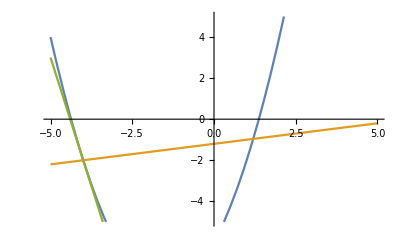

```mathematica
f[x_] := x^2 +3x -6
x0 =-4;
kt = D[f[x],x]/.x->x0;
kn = -(1/kt);
y0 = f[x0];
n0 = y0 ;
Plot[{f[x],kn x-x0 *kn + n0,kt (x-x0) + n0},{x,-5,5},PlotRange->{-5,5}]
```

```mathematica
GrafNormale[f_,x0_,zac_,kon_]:=Module[{kt,kn,y0,n0},
kt = D[f[x],x]/.x->x0;
kn = -(1/kt);
y0 = f[x0];
n0 = y0 ;
Plot[{f[x],kn x-x0 *kn + n0,kt (x-x0) + n0},{x,zac,kon},PlotRange->{zac,kon},Epilog->Disk[{x0,y0},0.1]
]]
```

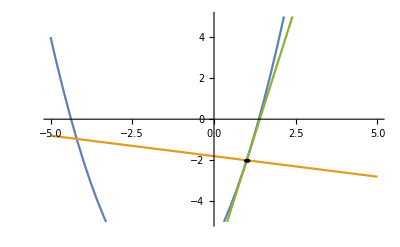

```mathematica
GrafNormale[f,1,-5,5]
```

Naloge:

1.
Nariši normalo na graf funkcije f [ x ] = 2 ^ ( -x / 2 ) v presečišču grafa funkcije f in premice z
enačbo y = √2.

```mathematica
ClearAll[f,g]
f[x_]:=2^(-x/2)
g[x_]:= Sqrt[2]
```

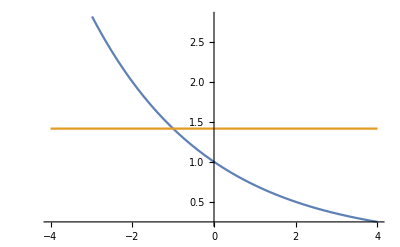

```mathematica
Plot[{f[x],g[x]},{x,-4,4}]
```

```mathematica
f[-1]
```

√2

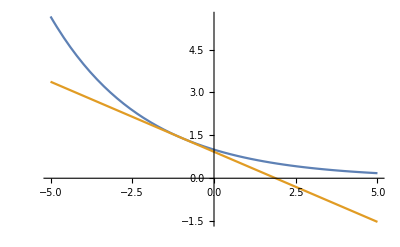

```mathematica
OdvodVTočki[f,-1,-5,5]
```

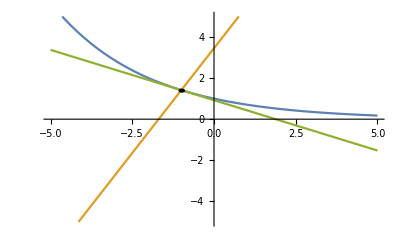

```mathematica
GrafNormale[f,-1,-5,5]
```

2.
Dokaži, da sta tangenti grafa f v točki, kjer f seka x-os pravokotni.

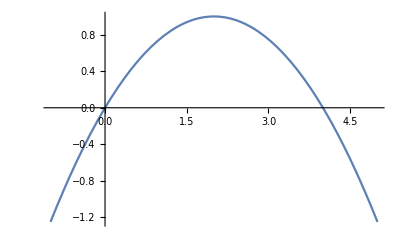

```mathematica
ClearAll[f]
f[x_]:=-x^2/4 + x
Plot[f[x],{x,-1,5}]
```

```mathematica
ničli = Solve[f[x] == 0,x];
ničla1 =x/. ničli//First
ničla2 = x/.ničli//Last
```

0

4

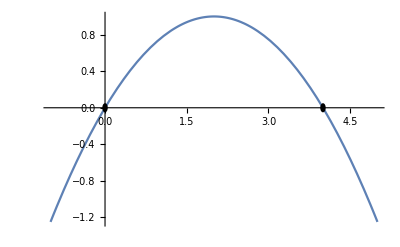

```mathematica
Plot[f[x],{x,-1,5},Epilog->{Disk[{ničla1,0},0.05],Disk[{ničla2,0},0.05]}]
```

```mathematica
EnacbaTangente[f];
tan1 = EnacbaTangente[f]/.a->0;
tan2 = EnacbaTangente[f]/.a->4;
presTan1Tan2 =x/. Solve[tan1 == tan2,x]//First
y =tan1/.x->presTan1Tan2
```

2

2

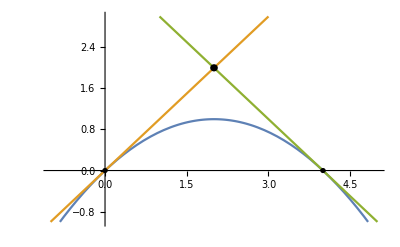

```mathematica
Plot[{f[x],tan1,tan2},{x,-1,5},Epilog->{Disk[{ničla1,0},0.05],Disk[{ničla2,0},0.05],Disk[{presTan1Tan2,y},0.07]},PlotRange->{-1,3}]
```